Stopping Times

```mathematica
demandProcess[x0_,t_,μ_,σ_]:=x0 Exp[(μ-σ^2/2)t+σ RandomVariate[NormalDistribution[0,Sqrt[t]]]];
```

```mathematica
stopTime[timeStep_,xthreshold_,x0_,μ_,σ_]:=Module[{stop,t,X},
stop=0; (* hasn't stopped *)
t=0.001;
X={x0};
While[Last[X]<xthreshold,
X=Append[X,demandProcess[x0,t,μ,σ]];
t=t+timeStep];
t];
```

```mathematica
stopTimemod[timeStep_,xthreshold_,x0_,μ_,σ_,horizon_]:=Module[{stop,t,X},
(* stop=0; hasn't stopped *)
t=0;
X={x0};
While[Last[X]<xthreshold &&t ≤horizon,
t=t+timeStep;
X=Append[X,demandProcess[x0,t,μ,σ]];
];
X=Append[X,Table[demandProcess[x0,t+timeStep*i,μ,σ],{i,horizon-t}]];
{t,Flatten@X}];
```

```mathematica
generalStopTime[Xmin_,Xmax_, xStep_,NsamplePaths_,timeStep_,xthreshold_,μ_,σ_]:=
Module[{x0=Xmin,
stop={},
X={}
},
While[x0≤Xmax,
stop=Append[stop,Table[stopTime[timeStep,xthreshold,x0,μ,σ],{i,1,NsamplePaths}]];
X=Append[X,Table[x0,{i,1,NsamplePaths}]];
x0=x0+xStep;
];
{X,stop}
];
```

```mathematica
estTau[x0_,threshold_]:=Module[{b},
Table[
b =Table[
stopTimemod[timeStep,(*xB[μ,σ,r,θ,k,α,δ]*) threshold@σ,x0,μ,σ,horizon],{i,NsamplePaths}];
(*Print["Tempos de paragem=",First/@b];*)
If[Count[First/@b,horizon+timeStep] >0,
Print["(σ, # unended sample paths) = ",{σ,Count[First/@b,horizon+timeStep]}]
];
Mean[First/@b],
{σ,0.01,σMax,0.01}]
];
```

## Prob 1

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
xB[μ_,σ_,r_,θ_,k_,α_,δ_]:=(d1[μ,σ,r])/(d1[μ,σ,r]-1) δ (r-μ)/(θ- α k);
xC[μ_,σ_,r_,θ_,δ_]:=(d1[μ,σ,r]+1)/(d1[μ,σ,r]-1) δ (r-μ)/θ;
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
```

### Benchmark & Capacity Optimization Models:

{xB,xC}={0.0128124,0.0190623}

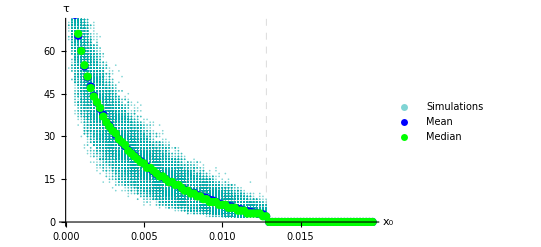
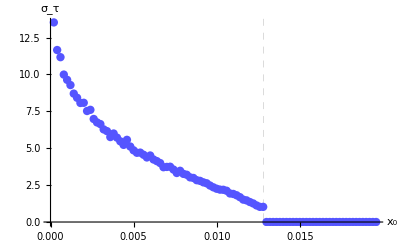
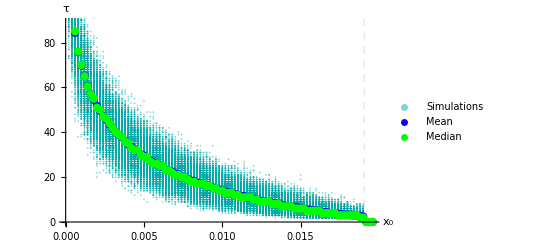
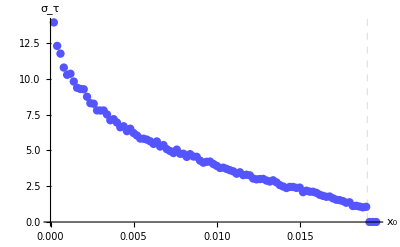

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k=100,
xStep=0.0002,
Xmin=0.0002,
Xmax,
NsamplePaths=1000,
timeStep=1,
trialBM,
trialCOM},
Print["{xB,xC}=",{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]}];
Xmax=Max[{xC[μ,σ,r,θ,δ],xB[μ,σ,r,θ,k,α,δ]}]+3*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xB[μ,σ,r,θ,k,α,δ],μ,σ];
trialCOM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xC[μ,σ,r,θ,δ],μ,σ];
{Show[
(* Benchmark Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xB[μ,σ,r,θ,k,α,δ],Dashed}},{}}
]
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xB[μ,σ,r,θ,k,α,δ],Dashed}},{}}],

(* Capacity Optimization Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialCOM[[1]],Flatten@trialCOM[[2]]},Transpose@{Mean/@trialCOM[[1]],Mean/@trialCOM[[2]]} ,Transpose@{Median/@trialCOM[[1]],Median/@trialCOM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{ Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xC[μ,σ,r,θ,δ],Dashed}},{}}
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialCOM[[1]],StandardDeviation/@trialCOM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xC[μ,σ,r,θ,δ],Dashed}},{}}]
}
]
```

### Volatility sensibility

```mathematica
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
NsamplePaths=500;
timeStep=1;
(*x0={0.001,0.01};*)

σMax=0.5;
horizon=1500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
estTauB001=estTau[0.001,Function[σ,xB[μ,σ,r,θ,k,α,δ]]];
estTauB01=estTau[0.01,Function[σ,xB[μ,σ,r,θ,k,α,δ]]];
estTauC001=estTau[0.001,Function[σ,xC[μ,σ,r,θ,δ]]];
estTauC01=estTau[0.01,Function[σ,xC[μ,σ,r,θ,δ]]];
```

(σ, # unended sample paths) = {0.38,4}

(σ, # unended sample paths) = {0.39,4}

(σ, # unended sample paths) = {0.4,9}

(σ, # unended sample paths) = {0.41,25}

(σ, # unended sample paths) = {0.42,41}

(σ, # unended sample paths) = {0.43,65}

(σ, # unended sample paths) = {0.44,77}

(σ, # unended sample paths) = {0.45,88}

(σ, # unended sample paths) = {0.46,135}

(σ, # unended sample paths) = {0.47,156}

(σ, # unended sample paths) = {0.48,184}

(σ, # unended sample paths) = {0.49,203}

(σ, # unended sample paths) = {0.5,233}

(σ, # unended sample paths) = {0.44,1}

(σ, # unended sample paths) = {0.45,1}

(σ, # unended sample paths) = {0.47,2}

(σ, # unended sample paths) = {0.48,1}

(σ, # unended sample paths) = {0.49,2}

(σ, # unended sample paths) = {0.5,4}

(σ, # unended sample paths) = {0.36,1}

(σ, # unended sample paths) = {0.37,3}

(σ, # unended sample paths) = {0.38,6}

(σ, # unended sample paths) = {0.39,14}

(σ, # unended sample paths) = {0.4,31}

(σ, # unended sample paths) = {0.41,66}

(σ, # unended sample paths) = {0.42,84}

(σ, # unended sample paths) = {0.43,111}

(σ, # unended sample paths) = {0.44,139}

(σ, # unended sample paths) = {0.45,151}

(σ, # unended sample paths) = {0.46,193}

(σ, # unended sample paths) = {0.47,211}

(σ, # unended sample paths) = {0.48,245}

(σ, # unended sample paths) = {0.49,287}

(σ, # unended sample paths) = {0.5,293}

(σ, # unended sample paths) = {0.44,1}

(σ, # unended sample paths) = {0.45,1}

(σ, # unended sample paths) = {0.46,6}

(σ, # unended sample paths) = {0.47,7}

(σ, # unended sample paths) = {0.48,9}

(σ, # unended sample paths) = {0.49,10}

(σ, # unended sample paths) = {0.5,15}

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC01}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xB[μ,σ,r,θ,k,α,δ],xC[μ,σ,r,θ,δ]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_B^*","x_C^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
Plot[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],{σ,0.01,σMax},
AxesOrigin->{0,0},
AxesLabel->{"σ","K^*"},
PlotStyle->Brown],
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB001,1]-Drop[estTauB001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB01,1]-Drop[estTauB01,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC001,1]-Drop[estTauC001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC01,1]-Drop[estTauC01,-1])},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xC[μ,σ+0.01,r,θ,δ]-xC[μ,σ,r,θ,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xC[μ,σ+0.01,r,θ,δ]]-Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
(* % variation *)
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

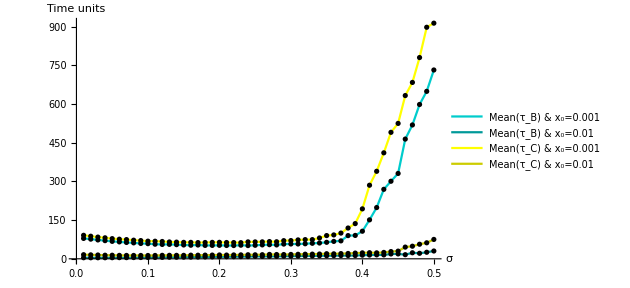
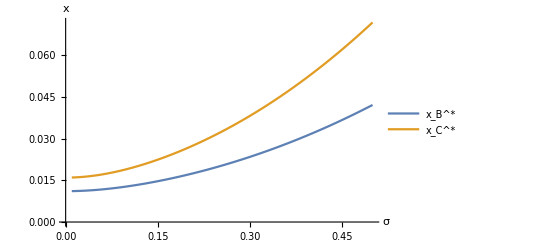
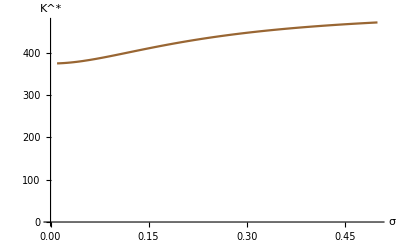
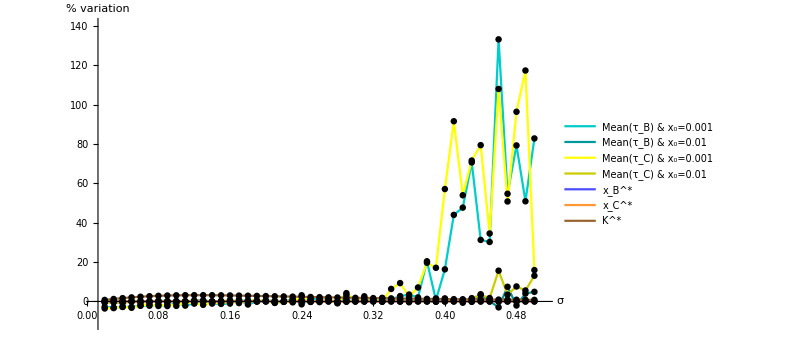

```mathematica
(* % varitation up to σ=0.35 *)
Module[{σMax=0.35},
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC001,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC01,1]-Drop[estTauC01,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xC[μ,σ+0.01,r,θ,δ]-xC[μ,σ,r,θ,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xC[μ,σ+0.01,r,θ,δ]]-Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

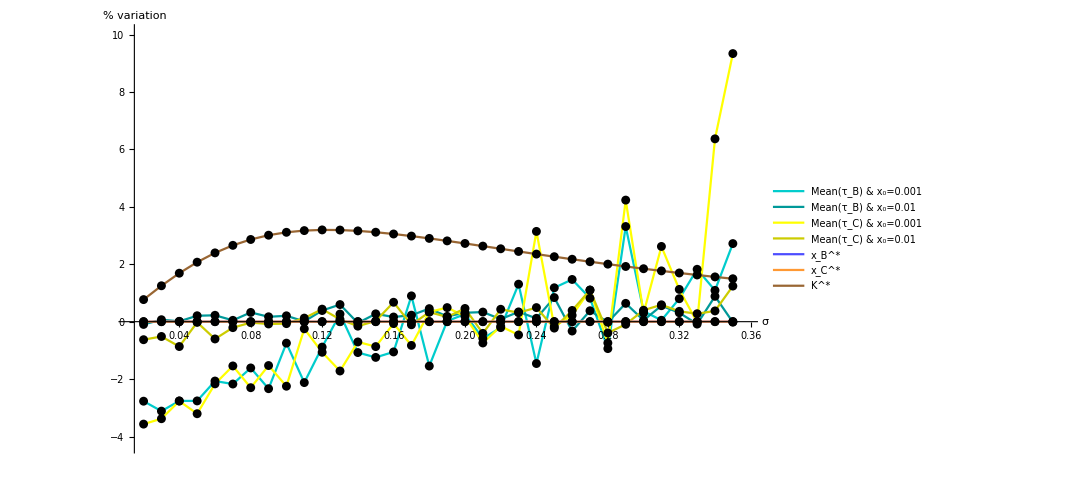

Tabela representativa:

```mathematica
(* Usar sse avaliar a value function *)
h[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=(θ- α k) k *x/(r-μ)-δ k;
aB[x_,μ_,σ_,r_,θ_,k_,α_,δ_]:=((θ- α k) k *x/(r-μ)-δ k)*x^(-d1[μ,σ,r]);
hC[x_,r_,μ_,σ_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x);
aC[x_,μ_,σ_,r_,θ_,α_,δ_]:=(x θ-δ (r-μ))^2/(4 α (r-μ)x)*x^(-d1[μ,σ,r]);

FxB[x_,r_,μ_,σ_,θ_,α_,δ_,k_]:=If[x<xB[μ,σ,r,θ,k,α,δ],
aB[xB[μ,σ,r,θ,k,α,δ],μ,σ,r,θ,k,α,δ]*x^(d1[μ,σ,r]),
h[x,r,μ,σ,θ,α,δ,k]];
FxC[x_,r_,μ_,σ_,θ_,α_,δ_]:=If[x<xC[μ,σ,r,θ,δ],
aC[xC[μ,σ,r,θ,δ],μ,σ,r,θ,α,δ]*x^(d1[μ,σ,r]),
hC[x,r,μ,σ,θ,α,δ]];
```

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],
Join[{" ", "K^*"},Map[Function[σ,NumberForm[Kopt[μ,r,θ,α,δ,xC[μ,σ,r,θ,δ]],5]],Δ]],

Join[{" ", "x_B^*"},Map[Function[σ,NumberForm[xB[μ,σ,r,θ,k,α,δ],2]],Δ]],
Join[{" ", "x_C^*"},Map[Function[σ,NumberForm[xC[μ,σ,r,θ,δ],2]],Δ]],

Join[{0.001, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.001, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC001[[Flatten@Position[part,elem]]]],Δ]],
(*Prepend[Map[Function[σ,NumberForm[FxB[0.001,r,μ,σ,θ,α,δ,k],2]],Δ],"F_B"],
Prepend[Map[Function[σ,NumberForm[FxC[0.001,r,μ,σ,θ,α,δ],2]],Δ],"F_C"],*)

Join[{0.01, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC01[[Flatten@Position[part,elem]]]],Δ]]
(*Prepend[Map[Function[σ,NumberForm[FxB[0.01,r,μ,σ,θ,α,δ,k],2]],Δ],"F_B"],
Prepend[Map[Function[σ,NumberForm[FxC[0.01,r,μ,σ,θ,α,δ],2]],Δ],"F_C"]*)
},
Dividers->{{2->True,3->True},{1->True,2->True,-5->True,-3->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | K^* | 381.04 | 395.08 | 410.92 | 425.39 | 437.62 | 447.66 | 455.8 | 462.41
  | x_B^* | 0.012 | 0.013 | 0.015 | 0.017 | 0.02 | 0.023 | 0.027 | 0.032
  | x_C^* | 0.017 | 0.019 | 0.022 | 0.027 | 0.032 | 0.038 | 0.045 | 0.053
0.001 | OverBar[τ_B] | 66.924 | 58.348 | 53.796 | 52.042 | 52.658 | 52.734 | 62.532 | 136.436
0.001 | OverBar[τ_C] | 79.19 | 69.346 | 64.95 | 62.368 | 66.044 | 69.63 | 83.046 | 176.542
0.01 | OverBar[τ_B] | 4.348 | 5.366 | 6.5 | 7.368 | 9.318 | 10.266 | 11.876 | 13.502
0.01 | OverBar[τ_C] | 13.736 | 12.992 | 13.474 | 14.406 | 15.68 | 17.524 | 20.45 | 21.984

## Prob 1I

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
xPos[r_,μ_, σ_,θ_,k0_,α_,δ_]:=1/((-1+d1[μ,σ,r]) r θ^2)(-d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2));
Kopt[μ_,r_,θ_,α_,δ_,x_]:=(θ x-δ(r-μ))/(2 α x);
```

### Benchmark & Capacity Optimization Models:

{xB,xC}={0.0243435,0.024042}

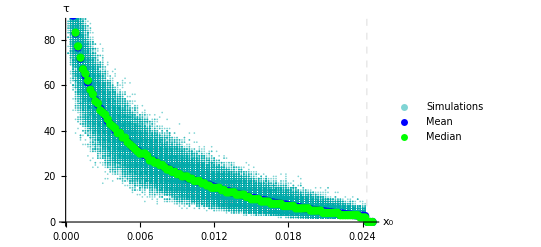
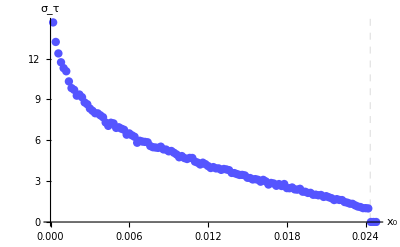
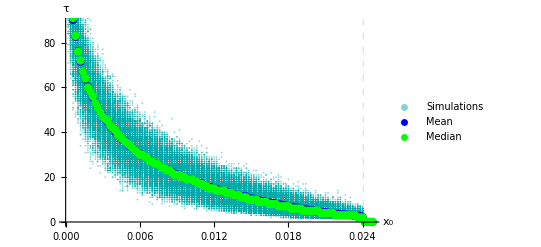
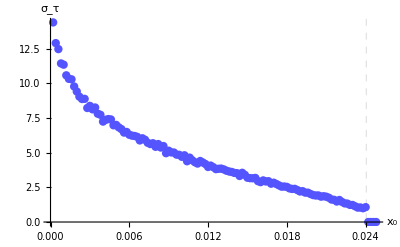

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k0=90,
k=100,
xStep=0.0002,
Xmin=0.0002,
Xmax,
NsamplePaths=1000,
timeStep=1,
trialBM,
trialCOM},
Print["{xB,xC}=",{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]}];
Xmax=Max[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]}]+3*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xxB[r,μ, σ,θ,k0,α,δ,k],μ,σ];
trialCOM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xPos[r,μ, σ,θ,k0,α,δ],μ,σ];
{Show[
(* Benchmark Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xxB[r,μ, σ,θ,k0,α,δ,k],Dashed}},{}}
]
],
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xxB[r,μ, σ,θ,k0,α,δ,k],Dashed}},{}}],

(* Capacity Optimization Model *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialCOM[[1]],Flatten@trialCOM[[2]]},Transpose@{Mean/@trialCOM[[1]],Mean/@trialCOM[[2]]} ,Transpose@{Median/@trialCOM[[1]],Median/@trialCOM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{ Right,Top}],
AxesLabel->{"x_0","τ"},
GridLines->{{{xPos[r,μ, σ,θ,k0,α,δ],Dashed}},{}}
], 
(* Standard deviation *)
 ListPlot[Transpose@{Mean/@trialCOM[[1]],StandardDeviation/@trialCOM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xPos[r,μ, σ,θ,k0,α,δ],Dashed}},{}}]
}
]
```

### Volatility sensibility

```mathematica
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
timeStep=1;

σMax=0.5;
(* horizon=1000; 
NsamplePaths=100; *)

horizon=1500; 
NsamplePaths=500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
Parallelize[ estTauB001=estTau[0.001,Function[σ,xxB[r,μ, σ,θ,k0,α,δ,k]]]];
Parallelize[ estTauB01=estTau[0.01,Function[σ,xxB[r,μ, σ,θ,k0,α,δ,k]]] ];
Parallelize[ estTauC001=estTau[0.001,Function[σ,xPos[r,μ, σ,θ,k0,α,δ]]] ];
Parallelize[ estTauC01=estTau[0.01,Function[σ,xPos[r,μ, σ,θ,k0,α,δ]]] ];
```

(σ, # unended sample paths) = {0.36,2}

(σ, # unended sample paths) = {0.37,10}

(σ, # unended sample paths) = {0.38,11}

(σ, # unended sample paths) = {0.39,24}

(σ, # unended sample paths) = {0.4,49}

(σ, # unended sample paths) = {0.41,57}

(σ, # unended sample paths) = {0.42,79}

(σ, # unended sample paths) = {0.43,123}

(σ, # unended sample paths) = {0.44,161}

(σ, # unended sample paths) = {0.45,190}

(σ, # unended sample paths) = {0.46,218}

(σ, # unended sample paths) = {0.47,256}

(σ, # unended sample paths) = {0.48,256}

(σ, # unended sample paths) = {0.49,264}

(σ, # unended sample paths) = {0.5,316}

(σ, # unended sample paths) = {0.44,2}

(σ, # unended sample paths) = {0.45,1}

(σ, # unended sample paths) = {0.46,4}

(σ, # unended sample paths) = {0.47,8}

(σ, # unended sample paths) = {0.48,12}

(σ, # unended sample paths) = {0.49,20}

(σ, # unended sample paths) = {0.5,34}

(σ, # unended sample paths) = {0.37,3}

(σ, # unended sample paths) = {0.38,15}

(σ, # unended sample paths) = {0.39,23}

(σ, # unended sample paths) = {0.4,43}

(σ, # unended sample paths) = {0.41,63}

(σ, # unended sample paths) = {0.42,88}

(σ, # unended sample paths) = {0.43,128}

(σ, # unended sample paths) = {0.44,164}

(σ, # unended sample paths) = {0.45,203}

(σ, # unended sample paths) = {0.46,221}

(σ, # unended sample paths) = {0.47,242}

(σ, # unended sample paths) = {0.48,283}

(σ, # unended sample paths) = {0.49,291}

(σ, # unended sample paths) = {0.5,298}

(σ, # unended sample paths) = {0.43,3}

(σ, # unended sample paths) = {0.44,1}

(σ, # unended sample paths) = {0.45,6}

(σ, # unended sample paths) = {0.46,4}

(σ, # unended sample paths) = {0.47,14}

(σ, # unended sample paths) = {0.48,13}

(σ, # unended sample paths) = {0.49,27}

(σ, # unended sample paths) = {0.5,32}

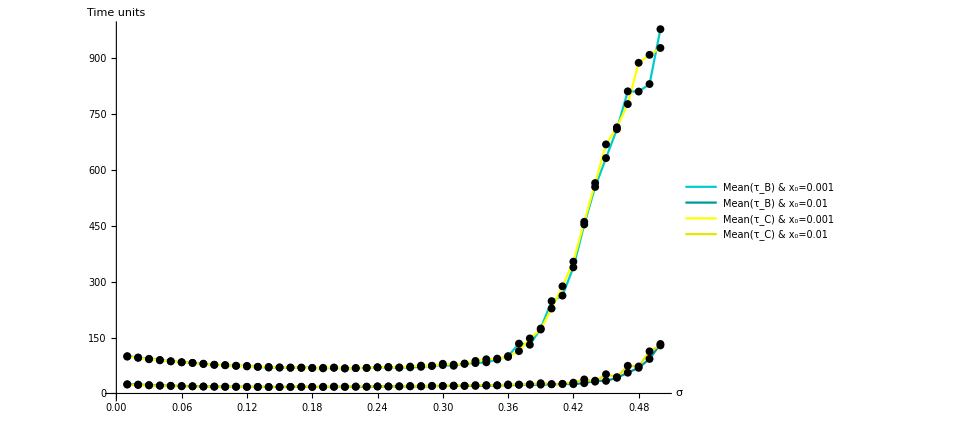
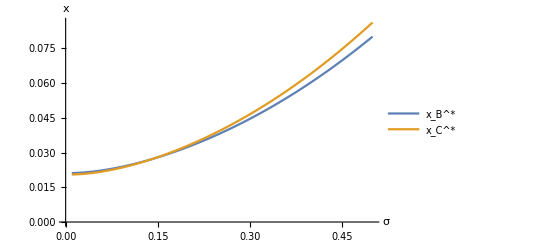
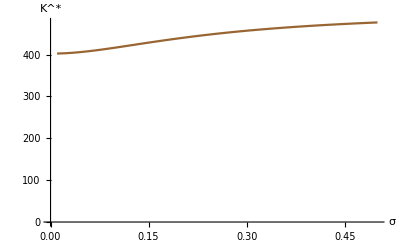
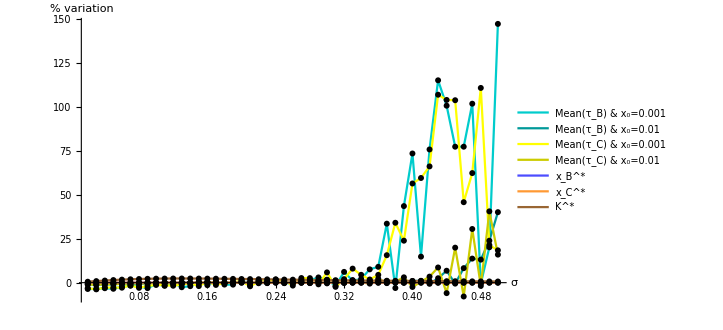

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauC01}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.1]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_B^*","x_C^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
Plot[Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]],{σ,0.01,σMax},
AxesOrigin->{0,0},
AxesLabel->{"σ","K^*"},
PlotStyle->Brown],
(* % variation *)
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB001,1]-Drop[estTauB001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauB01,1]-Drop[estTauB01,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC001,1]-Drop[estTauC001,-1])},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],(Drop[estTauC01,1]-Drop[estTauC01,-1])},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xPos[r,μ, σ+0.01,θ,k0,α,δ]-xPos[r,μ, σ,θ,k0,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xPos[r,μ, σ+0.01,θ,k0,α,δ]]-Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2],Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Left,Top}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

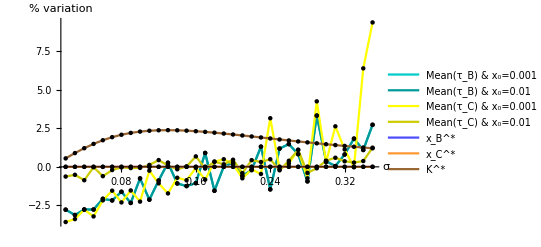

```mathematica
(* % variation up to σ=0.35 *)
Module[{σMax=0.35},
ListPlot[
{Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC001,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauC01,1]-Drop[estTauC01,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xB[μ,σ+0.01,r,θ,k,α,δ]-xB[μ,σ,r,θ,k,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xPos[r,μ, σ+0.01,θ,k0,α,δ]-xPos[r,μ, σ,θ,k0,α,δ])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(Kopt[μ,r,θ,α,δ,xPos[r,μ, σ+0.01,θ,k0,α,δ]]-Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Yellow,Darker[Yellow,0.2], Lighter[Blue,0.3],Lighter[Orange,0.2],Brown},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_C) & x_0=0.001",
"Mean(τ_C) & x_0=0.01",
"x_B^*","x_C^*","K^*" },{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

Tabela representativa:

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],
Join[{" ", "K^*"},Map[Function[σ,NumberForm[Kopt[μ,r,θ,α,δ,xPos[r,μ, σ,θ,k0,α,δ]],5]],Δ]],

Join[{" ", "x_B^*"},Map[Function[σ,NumberForm[xxB[r,μ, σ,θ,k0,α,δ,k],2]],Δ]],
Join[{" ", "x_C^*"},Map[Function[σ,NumberForm[xPos[r,μ, σ,θ,k0,α,δ],2]],Δ]],

Join[{0.001, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.001, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC001[[Flatten@Position[part,elem]]]],Δ]],

Join[{0.01, "OverBar[τ_B]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_C]"},N@Flatten@Map[Function[elem,estTauC01[[Flatten@Position[part,elem]]]],Δ]]
},
Dividers->{{2->True,3->True},{1->True,2->True,-5->True,-3->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | K^* | 406.62 | 416.81 | 428.59 | 439.6 | 449.1 | 457.01 | 463.51 | 468.84
  | x_B^* | 0.022 | 0.024 | 0.028 | 0.033 | 0.038 | 0.045 | 0.052 | 0.06
  | x_C^* | 0.021 | 0.024 | 0.028 | 0.033 | 0.039 | 0.047 | 0.055 | 0.064
0.001 | OverBar[τ_B] | 67.64 | 58.706 | 53.644 | 52.224 | 52.46 | 57.49 | 63.972 | 106.982
0.001 | OverBar[τ_C] | 78.21 | 68.426 | 63.82 | 63.938 | 65.552 | 70.664 | 90.086 | 193.648
0.01 | OverBar[τ_B] | 4.294 | 5.258 | 6.478 | 7.814 | 9.532 | 10.254 | 11.902 | 14.154
0.01 | OverBar[τ_C] | 13.884 | 12.892 | 13.4 | 14.924 | 15.526 | 16.93 | 19.768 | 23.112

## Prob III

```mathematica
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2]; 

xxB1[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])(δ k(r-μ))/((θ- α k) k -2η k0 k); (* x_1,A *) 
xxB2[r_,μ_, σ_,θ_,k0_,α_,δ_,k_,η_]:=(d1[μ,σ,r] (1-k0 α) (r-μ))/(2 (-1+d1[μ,σ,r] ) k r η); (* x_2 *)
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k; (* x_1,R ; não utilizada para análise -> Prob II *)
```

### Benchmark Model with 2 stopping times (simultaneous prod & replace) :

Existe produção simultânea, logo dois tempos de paragem.

{x1A,x2,x1R}={1.10099,6.57153,3.79792}

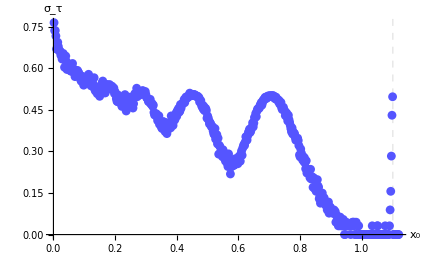
{-Graphics-,-Graphics-,  | τ_2 |  
Mean | Median | Std. Dev.
5.486 | 5.001 | 0.765115}

```mathematica
SeedRandom[1];
Module[
{σ=0.1,
μ=0.45,
r=0.85,
δ=0.95,
α=0.015,
θ=1.5,
k0=51.5,
k=2.5,
xStep=0.002,
Xmin=0.002,
Xmax,
NsamplePaths=1000,
timeStep=1,
(* η={0.007,0.012,0.013},*)
trialBM,
trialBM2,
η=0.007},
If[η<(1-α k0)(θ-α k)/(2(δ k r+ (1-α k0)k0)) (* η* *),
Print["Existe produção simultânea, logo dois tempos de paragem."],
Print["Não existe produção simultânea, logo um único tempo de paragem - ver Prob II."]
];
Print["{x1A,x2,x1R}=",{xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB2[r,μ, σ,θ,k0,α,δ,k,η],xxB[r,μ, σ,θ,k0,α,δ,k]}];
Xmax=xxB1[r,μ, σ,θ,k0,α,δ,k,η]+10*xStep;
trialBM=generalStopTime[Xmin,Xmax, xStep,NsamplePaths,timeStep,xxB1[r,μ, σ,θ,k0,α,δ,k,η],μ,σ];
trialBM2=generalStopTime[xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB1[r,μ, σ,θ,k0,α,δ,k,η], xStep,NsamplePaths,timeStep,xxB2[r,μ, σ,θ,k0,α,δ,k,η],μ,σ];
{
(* First stopping time *)
(* Mean & Median *)
ListPlot[{Transpose@{Flatten@trialBM[[1]],Flatten@trialBM[[2]]},Transpose@{Mean/@trialBM[[1]],Mean/@trialBM[[2]]} ,Transpose@{Median/@trialBM[[1]],Median/@trialBM[[2]]}},
PlotStyle->{{Darker[Cyan],Opacity[.5],PointSize[0.003]},{Blue,PointSize[0.015]},{Green,PointSize[0.015]}} ,
PlotLegends->Placed[{"Simulations","Mean","Median"},{Right,Top}],
AxesLabel->{"x_0","τ"},
PlotRange->All,
GridLines->{{{xxB1[r,μ, σ,θ,k0,α,δ,k,η],Dashed}},{}}
],
(* Standard deviation *)
ListPlot[Transpose@{Mean/@trialBM[[1]],StandardDeviation/@trialBM[[2]]},PlotStyle->{Lighter[Blue],PointSize[0.015]},
AxesLabel->{"x_0","σ_τ"},
GridLines->{{{xxB1[r,μ, σ,θ,k0,α,δ,k,η],Dashed}},{}}],
(* Second stopping time *)
Grid[{{" ","τ_2"," "},
{(* "x_(1, A)^*","x_2^*",*) "Mean" ,"Median","Std. Dev."},
{Mean@trialBM2[[2,1]],Median@trialBM2[[2,1]],StandardDeviation@trialBM[[2,1]]} 
},
Dividers->{{},{1->True,2->True,-1->True}} 
]
}
]
```

### Volatility sensibility

```mathematica
μ=0.45;
r=0.85;
δ=0.95;
α=0.015;
θ=1.5;
k0=51.5;
k=2.5;
η=0.007;
timeStep=1;

σMax=0.5;
(* horizon=1000; 
NsamplePaths=100; *)

horizon=1500; 
NsamplePaths=500;
```

Plots para σ∈(0.001,0.5) considerando x0∈{0.001,0.01} :

```mathematica
estTauB001=estTau[0.001,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]]];
estTauB01=estTau[0.01,Function[σ,xxB1[r,μ, σ,θ,k0,α,δ,k,η]]];
estTauB2=Table[
b =Table[
stopTimemod[timeStep,xxB2[r,μ, σ,θ,k0,α,δ,k,η],xxB1[r,μ, σ,θ,k0,α,δ,k,η],μ,σ,horizon],{i,NsamplePaths}];
If[Count[First/@b,horizon+timeStep] >0,
Print["(σ_B, # unended sample paths) = ",{σ,Count[First/@b,horizon+timeStep]}]
];
Mean[First/@b],
{σ,0.01,σMax,0.01}];
```

```mathematica
{
(* Mean optimal investment times *)
ListPlot[{Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB001},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB01},
Transpose@{Table[σ,{σ,0.01,σMax,0.01}],estTauB2}},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_2)"},{Left,Top}],
AxesLabel->{"σ","Time units"},
Joined->True,
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1]},
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
],
(* Demand thresholds *)
Plot[{xxB1[r,μ, σ,θ,k0,α,δ,k,η],xxB2[r,μ, σ,θ,k0,α,δ,k,η]},{σ,0.01,σMax},
AxesOrigin->{0,0},
PlotLegends->Placed[{"x_(1, A)^*","x_2^*"},{Left,Top}],
AxesLabel->{"σ","x"}],
(* % variation *)
ListPlot[
{
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB2,1]-Drop[estTauB2,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xxB1[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB1[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xxB2[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB2[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1], Lighter[Blue,0.3],Lighter[Orange,0.2]},
PlotLegends->Placed[{"Mean(τ_(1, A)) & x_0=0.001","Mean(τ_(1, A)) & x_0=0.01",
"Mean(τ_2)","x_(1, A)^*","x_2^*"},{Left,Bottom}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
}
```

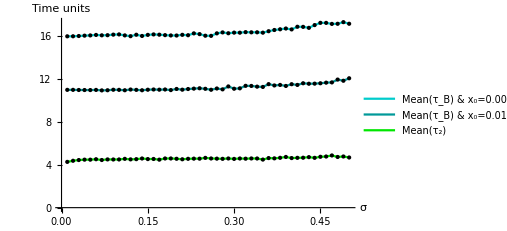
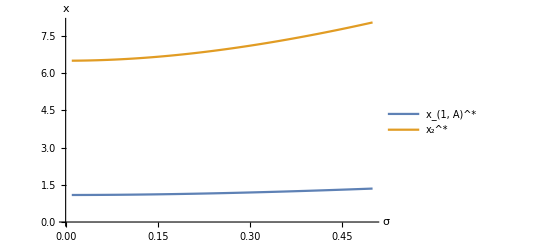
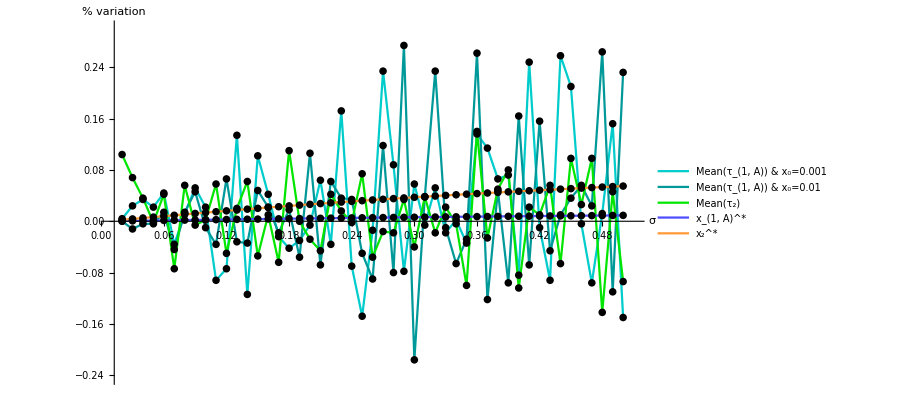

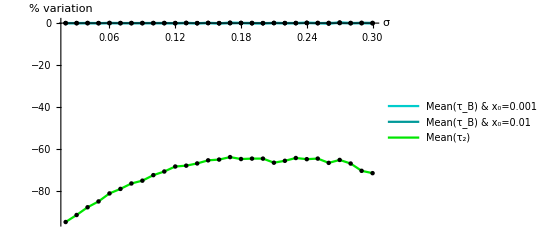

```mathematica
(* % varitation up to σ=0.3 *)
Module[{σMax=0.30},
ListPlot[
 {Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB001,1]-Drop[estTauB001,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB01,1]-Drop[estTauB01,-1]),(σMax-0.01)/0.01]},
Transpose@{Table[σ,{σ,0.02,σMax,0.01}],Take[(Drop[estTauB2,1]-Drop[estTauC001,-1]),(σMax-0.01)/0.01]},
Table[{σ+0.01,(xxB1[r,μ, σ+0,01,θ,k0,α,δ,k,η]-xxB1[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}],
Table[{σ+0.01,(xxB2[r,μ, σ+0.01,θ,k0,α,δ,k,η]-xxB2[r,μ, σ,θ,k0,α,δ,k,η])},{σ,0.01,σMax-0.01,0.01}]
},
PlotStyle->{Darker[Cyan,0.2],Darker[Cyan,0.4],Darker[Green,0.1]},
PlotLegends->Placed[{"Mean(τ_B) & x_0=0.001","Mean(τ_B) & x_0=0.01",
"Mean(τ_2)" },,{Scaled[{0,0.5}], {0, 0.5}}],
AxesLabel->{"σ","% variation"},
Joined->True,
PlotRange->All,
Mesh->All,
MeshStyle->PointSize[0.008]
]
]
```

Tabela representativa:

```mathematica
Δ=Table[i,{i,0.05,0.4,0.05}];
part=Table[σ,{σ,0.01,σMax,0.01}];
Grid[{
 Join[{"x_0"," σ "},Δ],

Join[{" ", "x_(1, A)^*"},Map[Function[σ,NumberForm[xxB1[r,μ, σ,θ,k0,α,δ,k,η],2]],Δ]],
Join[{" ", "x_2^*"},Map[Function[σ,NumberForm[xxB2[r,μ, σ,θ,k0,α,δ,k,η],2]],Δ]],

Join[{0.001, "OverBar[τ_(1, A)]"},N@Flatten@Map[Function[elem,estTauB001[[Flatten@Position[part,elem]]]],Δ]],
Join[{0.01, "OverBar[τ_(1, A)]"},N@Flatten@Map[Function[elem,estTauB01[[Flatten@Position[part,elem]]]],Δ]],

Join[{" ", "OverBar[τ_2]"},N@Flatten@Map[Function[elem,estTauB2[[Flatten@Position[part,elem]]]],Δ]]
},
Dividers->{{2->True,3->True},{1->True,2->True,-4->True,-2->True,-1->True}}
]
```

x_0 |  σ  | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4
  | x_(1, A)^* | 1.1 | 1.1 | 1.1 | 1.1 | 1.2 | 1.2 | 1.2 | 1.3
  | x_2^* | 6.5 | 6.6 | 6.7 | 6.8 | 6.9 | 7.1 | 7.3 | 7.5
0.001 | OverBar[τ_(1, A)] | 16.084 | 16.178 | 16.134 | 16.074 | 16.056 | 16.344 | 16.34 | 16.644
0.01 | OverBar[τ_(1, A)] | 10.98 | 11. | 11.012 | 11.084 | 11.098 | 11.104 | 11.272 | 11.528
  | OverBar[τ_2] | 4.48 | 4.5 | 4.536 | 4.564 | 4.648 | 4.552 | 4.49 | 4.63